# Mathematica在数理学习中的应用

张静宁 PB14203209 2016-8-14

## 前言

### 我们知道，合理运用 Mathematica 能给我们的学习提供很大帮助，比如验算作业、绘制函数图形建立直观感受、处理大学物理实验数据等等。无论是从实用的角度，还是为了加深对数学理论的理解，Mathematica 都非常值得我们学习。以下是本人近期初学时做的一些笔记。

## 微积分

### 求极限

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Limit[(1+x/n)^n,n->Infinity]
```

ⅇ^x

### 求导数

```mathematica
D[x^2,x] (*求一阶导 *)
```

2 x

```mathematica
D[Sin[x],{x,2}] (* 求二阶导 *)
```

-sin(x)

```mathematica
D[x^3 y+y^2,{{x,y}}] (* 分别求x,y偏导 *)
```

{3 x^2 y,x^3+2 y}

```mathematica
D[x^3 y+y^2,x,y] (* 对x求导完，在对y求导 *)
```

3 x^2

```mathematica
D[x^3 y+y^2,{{x,y},2}] (* 求海森矩阵 *)
```

(6 x y | 3 x^2
3 x^2 | 2)

### 自定义函数

```mathematica
f1[x_]:= x^2+x+1 (* 自定义单变量函数 *)
```

```mathematica
D[f1[a],a]  (* 求导 *)
```

2 a+1

```mathematica
f2[x_,y_]:= Sin[x y]/(x^2+y^2) (* 自定义多变量函数 *)
```

```mathematica
D[f2[x,y],x] (* 再求导 *)
```

(y cos(x y))/(x^2+y^2)-(2 x sin(x y))/((x^2+y^2)^2)

### 求积分

```mathematica
Integrate[1/(1-x^3), x] (* 不定积分 *)
```

1/6 log(x^2+x+1)-1/3 log(1-x)+(tan^-1((2 x+1)/(√3)))/(√3)

```mathematica
Integrate[x^2,{x,4,1}] (* 定积分 *)
```

-21

```mathematica
Integrate[x^2+y^2,{x,0,a},{y,0,b}] (* 重积分 *)
```

1/3 a b (a^2+b^2)

### 级数展开

```mathematica
Series[Exp[x],{x,0,10}] (* 在零点展开到10次 *)
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O(x^11)

```mathematica
Series[Cos[x]/x,{x,Pi,3}] (* 在x=π点展开到3次*)
```

-1/π+(x-π)/π^2+((π^2-2) (x-π)^2)/(2 π^3)+(1/π^4-1/(2 π^2)) (x-π)^3+O((x-π)^4)

### 微分方程

```mathematica
Solve[x^2+a x +1==0,x] (* 解方程 *)
```

{{x→1/2 (-√(a^2-4)-a)},{x→1/2 (√(a^2-4)-a)}}

```mathematica
Solve[x+y==2&&x-y==1] (* 解方程组 *)
```

{{x→3/2,y→1/2}}

#### 求解微分方程

```mathematica
DSolve[y'[x]+y[x] ==a Sin[x],y[x],x] (* 解一阶常微分方程 *)
```

{{y(x)→1/2 a (sin(x)-cos(x))+c_1 ⅇ^-x}}

```mathematica
DSolve[{y'[x]+y[x] ==a Sin[x],y[0]==0},y,x] (* 代入一个边界条件 *)
```

{{y→({x}↦-1/2 a ⅇ^-x (-ⅇ^x sin(x)+ⅇ^x cos(x)-1))}}

```mathematica
FullSimplify[y''[x]+y[x]^2/.%107] (* 用/.将解带入一个表达式 *)
```

{1/4 a ⅇ^(-2 x) (-2 ⅇ^x (-a sin(x)+a cos(x)-1)+ⅇ^(2 x) (a (-sin(2 x))+a-2 sin(x)+2 cos(x))+a)}

#### 求解波动方程的定解问题

```mathematica
weqn = D[u[x,t],{t,2}]== D[u[x,t],{x,2}] (* 波动方程 *)
```

u^(0,2)(x,t)==u^(2,0)(x,t)

```mathematica
ic = {u[x,0]== E^(-x^2),Derivative[0,1][u][x,0]==1}(* 初始条件 *)
```

{u(x,0)==ⅇ^(-x^2),u^(0,1)(x,0)==1}

```mathematica
DSolve[{weqn,ic},u,{x,t}] (* 求解波动方程的初值问题 *)
```

{{u→({x,t}↦1/2 (ⅇ^(-(x-t)^2)+ⅇ^(-(t+x)^2))+t)}}

## 绘图

### 函数可视化

```mathematica
Plot3D[Evaluate[u[x,t]/.%114],{x,-7,7},{t,0,4},PlotRange->All] (* 前面波动方程初值问题的图解 *)
```

-Graphics3D-

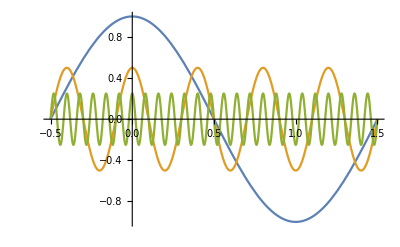

```mathematica
Plot[Tooltip[{Cos[Pi x],1/2 Cos[5 Pi x],1/4 Cos[25 Pi x]}],{x,-1/2,3/2}] (* 同时绘制多个函数 *)
```

### 图像的美化

```mathematica
vofPlot0 = Plot[Tooltip[{Cos[Pi x],Cos[Pi x]+1/2 Cos[5 Pi x],Cos[Pi x]+1/2 Cos[5 Pi x]+1/4 Cos[25 Pi x]}],{x,-1/2,3/2}];
```

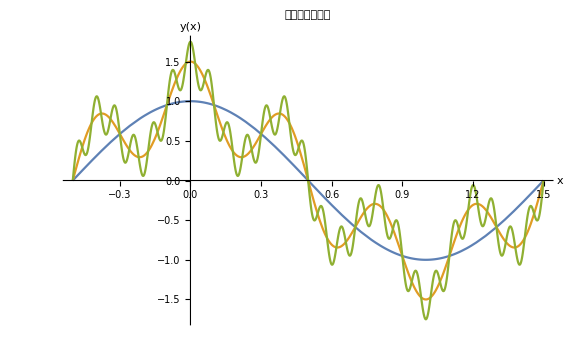

```mathematica
Show[vofPlot0,
AxesLabel->{Style["x",15,Bold],Style["y(x)",15,Bold]},
PlotLabel->Style["不可求导的函数",18,FontFamily->"Adobe Fan Heiti Std",Bold],
ImageSize->Large]
```

### 函数的切线

```mathematica
y[x_]:=2 x Sin[x];  (* 这里以一个函数为例*)
y[x]==y'[x] x+b/.x->Pi/2;
bRule=Solve[%,b][[1]]; (* 求出截距b *)
tangentY[x_]:=y'[a] x+b/.bRule/.a->Pi/2;  (* 求出切线方程 *)
```

```mathematica
tangentY[x]
```

2 x

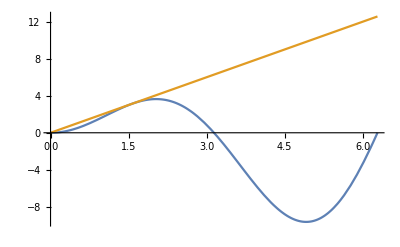

```mathematica
Plot[{y[x],tangentY[x]},{x,0,2Pi}] (* 画出原函数图像和切线 *)
```

## 处理实验数据

### 输入数据

```mathematica
data0 = Table[x^2,{x,1,20}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
data1={{0.00,0.00},{1.00,1.90},{2.00,4.41},{3.00,6.05},{4.00,7.85},{5.00,9.30},{6.00,11.83},{7.00,13.75},{8.00,16.72},{9.00,17.86}};
```

### 绘制曲线

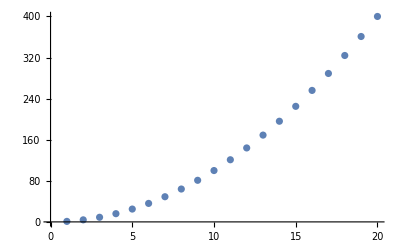

```mathematica
lpdata0 = ListPlot[data0]
```

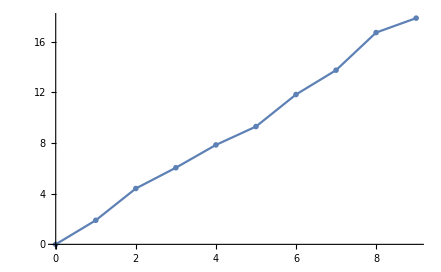

```mathematica
lpdata1 = ListPlot[data1,Joined->True,PlotMarkers->{Style["X",Bold]}] (* 把数据点连起来 *)
```

### 拟合曲线

```mathematica
fitdata1 = Fit[data1,{1,x},x]
```

1.99982 x-0.0321818

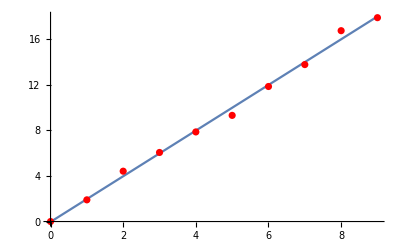

```mathematica
Show[Plot[fitdata1,{x,0,9}],ListPlot[data1,PlotStyle->Red]]
```

```mathematica
fitting = LinearModelFit[data1,{1,x,x^2},x]
```

FittedModel[0.0151515 x^2+1.86345 x+0.149636]

```mathematica
fitting["BestFit"]
```

0.0151515 x^2+1.86345 x+0.149636

```mathematica
fitting[{"RSquared","FitResiduals","ANOVATable"}]
```

{0.996406,{-0.149636,-0.128242,0.472848,0.173636,0.00412121,-0.545697,-0.0458182,-0.186242,0.69303,-0.288}, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 329.94 | 329.94 | 1940.18 | 8.11825×10^-10
x^2 | 1 | 0.121212 | 0.121212 | 0.712776 | 0.426432
Error | 7 | 1.1904 | 0.170056 |  | 
Total | 9 | 331.252 |  |  | }

### 导入数据及完整示例

```mathematica
epdata =Import["D:\\Mathematica\\Mathematica在数理学习中的应用示例\\ImportData.xlsx"] (* 导入一次实验的所有数据 *)
```

{{{Hg光谱测量值与标准值关系拟合图,},{测量值(nm),标准值(nm）},{364.97,365.02},{365.44,365.48},{366.29,366.3},{404.59,404.66},{407.75,407.78},{435.84,435.84},{545.97,546.07},{576.85,576.96},{578.92,579.07}}}

```mathematica
epdata1 = data[[1]][[3;;]] (* 提取出第一组数据 *)
```

{{364.97,365.02},{365.44,365.48},{366.29,366.3},{404.59,404.66},{407.75,407.78},{435.84,435.84},{545.97,546.07},{576.85,576.96},{578.92,579.07}}

```mathematica
fitepdata1 = Fit[data1,{1,x},x] (* 拟合曲线 *)
```

-0.139251+1.00045 x

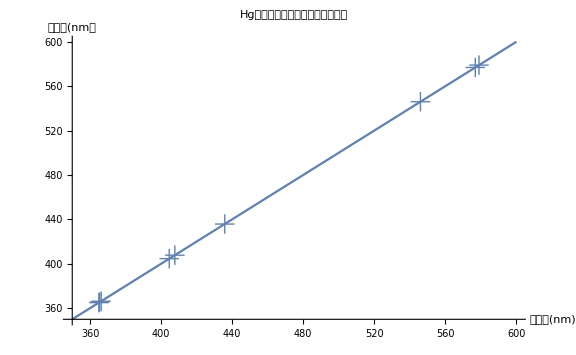

```mathematica
Show[Plot[fitepdata1,{x,350,600}],ListPlot[data1,PlotMarkers->{Style["+",20]}],
AxesLabel->{Style[epdata[[1]][[2]][[1]],15,Bold],Style[epdata[[1]][[2]][[2]],15,Bold]},
PlotLabel->Style[epdata[[1]][[1]][[1]],18,FontFamily->"Adobe Fan Heiti Std",Bold],
ImageSize->Large] (* 作图 *)
```

## 总结

#### Mathematica 在数理学习中的应用远远不止这些，这篇笔记中只初步讨论了微积分、绘图、数据处理三个部分。我们可以在今后的学习中进一步探索，我将会在github上面分享我的学习笔记与代码（链接）。

## 参考资料

1、中文视频：Mathematica 实用入门
2、中文教程：WhyMathematicaCH.nb
3、官方教程：Wolfram 参考资料